```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[Epi_,T_]:=1/(Exp[Epi/T]-1);
nbd1x[Epi_,T_]:=-1/T nb[Epi,T](nb[Epi,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
(*Epi[q_]:=√(q^2+mp2);*)
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B1thr[Epi_,mf2_,p0_,p_,q_,x_,T_,mu_]:=1/2(-nb[Epi[√(q^2+p^2-2p q x)],T]/Epi[√(q^2+p^2-2p q x)]*1/((ⅈ p0-mu+Epi[√(q^2+p^2-2p q x)])^2-Eq[q,mf2]^2)
-(nb[Epi[√(q^2+p^2-2p q x)],T]+1)/Epi[√(q^2+p^2-2p q x)]*1/((ⅈ p0-mu-Epi[√(q^2+p^2-2p q x)])^2-Eq[q,mf2]^2)
+nfa[mf2,q,T,mu]/Eq[q,mf2]*1/((ⅈ p0-mu-Eq[q,mf2])^2-Epi[√(q^2+p^2-2p q x)]^2)
+(nff[mf2,q,T,mu]-1)/Eq[q,mf2]*1/((ⅈ p0-mu+Eq[q,mf2])^2-Epi[√(q^2+p^2-2p q x)]^2));
F1B1q0thr[Epi_,mf2_,p0_,p_,q_,x_,T_,mu_]:=1/2 ⅈ (((ⅈ p0+Epi[√(p^2+q^2-2 p q x)]) nb[Epi[√(p^2+q^2-2 p q x)],T])/(Epi[√(p^2+q^2-2 p q x)] (-mu+ⅈ p0+Epi[√(p^2+q^2-2 p q x)]-Eq[q,mf2]) (-mu+ⅈ p0+Epi[√(p^2+q^2-2 p q x)]+Eq[q,mf2]))-((-ⅈ p0+Epi[√(p^2+q^2-2 p q x)]) (1+nb[Epi[√(p^2+q^2-2 p q x)],T]))/(Epi[√(p^2+q^2-2 p q x)] (mu-ⅈ p0+Epi[√(p^2+q^2-2 p q x)]-Eq[q,mf2]) (mu-ⅈ p0+Epi[√(p^2+q^2-2 p q x)]+Eq[q,mf2]))-((mu+Eq[q,mf2]) nfa[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[√(p^2+q^2-2 p q x)]^2+(mu-ⅈ p0+Eq[q,mf2])^2))+((-mu+Eq[q,mf2]) (-1+nff[mf2,q,T,mu]))/(Eq[q,mf2] (-Epi[√(p^2+q^2-2 p q x)]^2+(-mu+ⅈ p0+Eq[q,mf2])^2)));
Zpsip2[Epi_,mf2_,h_,p0_,p_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(4 π^2)NIntegrate[p q^3 x Re[F1B1thr[Epi,mf2,p0,p,q,x,T,mu]],{q,1,2000},{x,-1,1}]+(p^2)
mfp[Epi_,mf2_,h_,p0_,p_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(4 π^2)√mf2 NIntegrate[q^2 Re[F1B1thr[Epi,mf2,p0,p,q,x,T,mu]],{q,1,2000},{x,-1,1}]+√mf2
Zpsi0[Epi_,mf2_,h_,p0_,p_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(4 π^2)NIntegrate[q^2 Re[F1B1q0thr[Epi,mf2,p0,p,q,x,T,mu]],{q,1,2000},{x,-1,1}]/p0+1
```

# Import data

```mathematica
fpidata=Transpose[Import["../../../sigma0.dat"]];
q=Table[i,{i,1,2000,10}];
T=10;
sigmapi=Flatten[Table[Interpolation[Transpose[{q,√Flatten[Import["../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]]}]],{i,5,400,5}]];
mu=Flatten[Table[i*5.,{i,1,80,1}]];
```

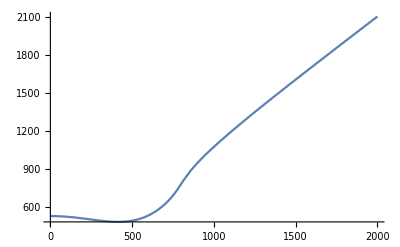

```mathematica
Plot[sigmapi[[80]][q],{q,1,2000}]
```

# Z_q spatial part

```mathematica
T=10;
sigmapi=Interpolation[Transpose[{q,√Flatten[Import["../input/T"<>ToString[T]<>"/sigma400.dat"]]}]];
dataZsp2=ParallelTable[Zpsip2[sigmapi,mf2[6.5,(fpidata[[T]][[80]])^2/2],6.5,π  T,i*10,T,400.],{i,1,200}];
(*Export["./T"<>ToString[T]<>"/Zpsi.dat",data]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
p2=Table[(i*10),{i,1,200}];
```

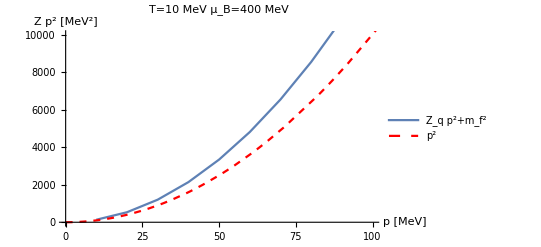

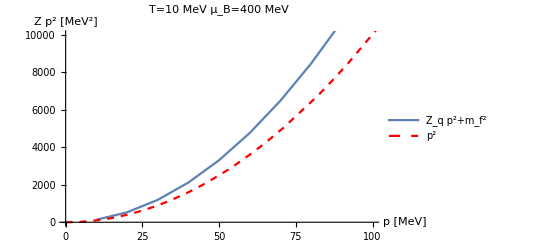

```mathematica
Show[ListLinePlot[Transpose[{p2,dataZsp2}],PlotLegends->{"Z_q p^2+m_f^2"}],Plot[x^2,{x,0,2000},PlotStyle->{Red,Dashed},PlotLegends->{"p^2"}],PlotRange->{{0,100},{0,1*10^4}},AxesLabel->{"p [MeV]","Z p^2 [MeV^2]"},PlotLabel->"T=10 MeV μ_B=400 MeV"]
```

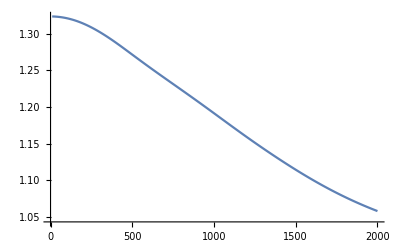

```mathematica
ListLinePlot[Transpose[{p2,dataZsp2/p2^2}]]
```

```mathematica
Export["./T10mu400/Zqs.dat",dataZsp2/p2^2]
```

./T10mu400/Zqs.dat

# m_q mass part

```mathematica
datamf=ParallelTable[mfp[sigmapi,mf2[6.5,(fpidata[[T]][[80]])^2/2],6.5,π  T,i*10,T,400.],{i,1,200}];
```

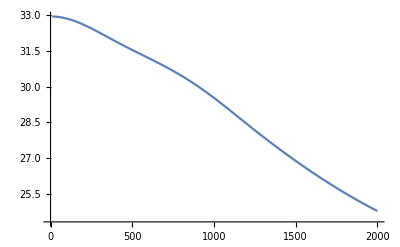

```mathematica
ListLinePlot[Transpose[{p2,datamf}]]
```

```mathematica
Export["./T10mu400/mf.dat",datamf]
```

./T10mu400/mf.dat

# Z_q temporal part

```mathematica
dataZ0=ParallelTable[Zpsi0[sigmapi,mf2[6.5,(fpidata[[T]][[80]])^2/2],6.5,π  T,i*10,T,400.],{i,1,200}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

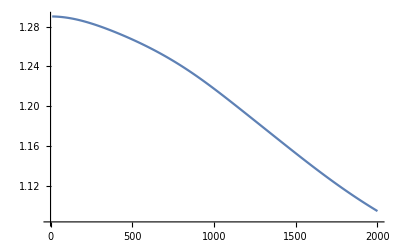

```mathematica
ListLinePlot[Transpose[{p2,dataZ0}]]
```

```mathematica
Export["./T10mu400/Zq0.dat",dataZ0]
```

./T10mu400/Zq0.dat